```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG];
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
```

{{g→InterpolatingFunction[{{0., 1.}}, <>]}}

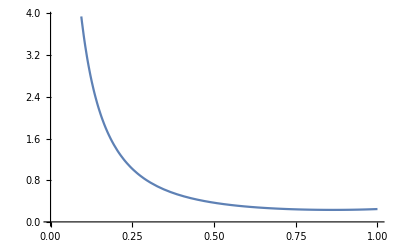

{5.01704}

{{0.0471997}}

{{0.0471997}}

0.0471997

```mathematica
Clear[blah,equilAUC,expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
blah=NDSolve[{0 == ( Ne α^2 / W) *x*(1-x)*D[g[x]*(1-2x),x]+1/2*x*(1-x)*D[g[x],{x,2}],
g[0]==θ,
g[1]==0}/.{W->fitVar, θ ->popMut,Ne->SourceNe},
g,{x,0,1},MaxStepSize->.000025]
Plot[g[x] /(x(1-x))/. blah ,{x,0,1}]
equilAUC = NIntegrate[Evaluate[g[x]/(x*(1-x)) /. blah],{x,0.00001,1}]
expectation = NIntegrate[Evaluate[g[x]/(equilAUC (1-x)) /. blah],{x,0.00001,1}]
Print[expectation]
expectation  = expectation[[1]][[1]]
```